```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
l=Flatten @ Import["test1-carry.dat"];
```

```mathematica
len=Length[l]
1./Sqrt[len]
```

65536

0.00390625

```mathematica
Mean[l]
StandardDeviation[l]
```

0.000450326

1.0406

{1.,0.00462104,-0.00018269,-0.00559067,-0.00667512,-0.00414431,0.00318368,-0.000301571,0.00186344,-0.00247479,-0.00161122,-0.00240302,0.000569315,0.00572515,0.00813713,-0.00290329,0.00308039,0.00919799,0.000783553,-0.00455681,0.00568158}

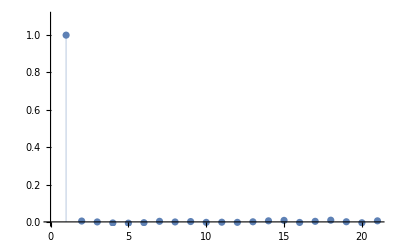

1.012

```mathematica
cf=CorrelationFunction[l,{20}]
ListPlot[cf,Filling->0,PlotRange->{0,1.1}]
Total[cf]
```

```mathematica
(* Allan variance estimate *)
diffs=Most[l]-Rest[l];
sqdiffs=diffs^2;
sumsqdiffs=Total[sqdiffs];
avar=sumsqdiffs/(2len)
adev=Sqrt[avar]
```

1.07781

1.03818

```mathematica
(* Convert to integers *)
lint=N@Round[l];
Mean[lint]
StandardDeviation[lint]
```

-0.000564575

1.07967

```mathematica
(* Allan variance estimate *)
diffs=Most[lint]-Rest[lint];
sqdiffs=diffs^2;
sumsqdiffs=Total[sqdiffs];
avar=sumsqdiffs/(2len)
adev=Sqrt[avar]
```

1.24333

1.11505

{1.,-0.0666425,0.00193708,-0.00511854,-0.00685954,-0.00404516,0.00239521,-0.00202924,0.00214654,-0.000864198,-0.00547196,-0.0028801,-0.00214705,0.00547146,0.00691138,-0.00447711,0.00221198,0.00962103,0.000117553,-0.00432004,0.0049478}

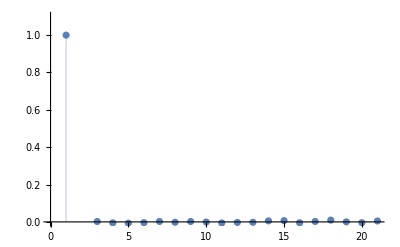

0.930905

```mathematica
cf=CorrelationFunction[N[lint],{20}]
ListPlot[cf,Filling->0,PlotRange->{0,1.1}]
Total[cf]
```

0.

{a→24189.,x0→-0.00446862,σ→1.08083}

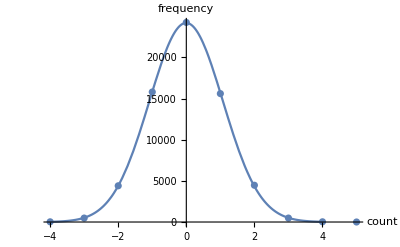

```mathematica
(* Distribution *)
ta=Tally[lint];
x0est=Sort[ta,#1[[2]]>#2[[2]]&][[1,1]]
p1=ListPlot[ta,AxesLabel->{"count","frequency"},LabelStyle->Larger];
fnc=a Exp[-(x-x0)^2/(2σ^2)];
sol=FindFit[ta,fnc,{{a,20000},{x0,x0est},{σ,1}},x]
fnc=fnc/.sol;
p2=Plot[fnc,{x,-4,4},PlotRange->All];
pp=Show[p1,p2]
```

1.00024

{1.,0.000713291,0.00217378,-0.00367577,0.00239026,0.0026896,-0.00510574,0.00636046,-0.000619787,0.00267004,0.000364056,-0.00378675,-0.00170054,-0.000501879,-0.00581269,0.00211814,0.0043455,-0.00388006,0.00424417,0.0038444,0.0062421}

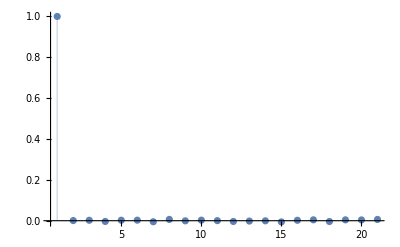

1.01307

```mathematica
(* LSB correlations *)
l2=Map[Mod[#,2]&,l];
Mean[l2]
cf=CorrelationFunction[l2,{20}]
ListPlot[cf,Filling->0,PlotRange->All]
Total[cf]
```